Previous Functions

```mathematica
Clear["Global`*"];
Ldynamics = 1/2 *(M+m)*x2^2 + 1/2 *m*l^2*θ2^2 + m*l*Cos[θ1]*x2*θ2 + m*g*l*Cos[θ1] - u*x1; (* Note: u is a scaled version of the original control by a factor of 1/(M+m)*)
fdot[s_] := D[s,x1]*x2 + D[s,x2]*x2dot + D[s,θ1]*θ2 + D[s,θ2]*θ2dot;
eqn1 = fdot[D[Ldynamics,x2]] - D[Ldynamics,x1];
eqn2 = fdot[D[Ldynamics,θ2]] - D[Ldynamics,θ1];
sol = Solve[{eqn1==0,eqn2 == 0},{x2dot,θ2dot}][[1]];
{x2dot,θ2dot} = {x2dot,θ2dot}/.sol ;
fx = {x2,x2dot,θ2,θ2dot};
x = {x1,x2,θ1,θ2};
λ = {λ1,λ2,λ3,λ4};
```

```mathematica
Clear["Global`*"]; (* Fix Bugs here *)
Ldynamics = 1/2 *(M+m)*x2^2 + 1/2 *m*l^2*θ2^2 + m*l*Cos[θ1]*x2*θ2 + m*g*l*Cos[θ1] - u*x1; (* Note: u is a scaled version of the original control by a factor of 1/(M+m)*)
fdot[s_] := D[s,x1]*x2 + D[s,x2]*x2dot + D[s,θ1]*θ2 + D[s,θ2]*θ2dot;
eqn1 = fdot[D[Ldynamics,x2]] - D[Ldynamics,x1];
eqn2 = fdot[D[Ldynamics,θ2]] - D[Ldynamics,θ1];
sol = Solve[{eqn1==0,eqn2 == 0},{x2dot,θ2dot}][[1]];
{x2dot,θ2dot} = {x2dot,θ2dot}/.sol ;
fx = {x2,x2dot,θ2,θ2dot};

ffCartPendulum[n_,τ_,τ1_,m_,M_,g_,l_]:=Module[{x1,x2,f,x,λ,θ1,θ2,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,x1ff,x2ff,x1ff0,x2ff0,θ1ff0,θ2ff0,uff0,θ1ff,θ2ff,uff,Ldynamics,L},Δt=τ/n;
x = {x1,x2,θ1,θ2};
λ = {λ1,λ2,λ3,λ4};
L = 1/2*u^2; (*Cost function*)
eqn = D[fx,u].λ + D[L,u];
sol = Solve[{eqn==0},{u}][[1]];
{u} = {u}/.sol ;
For[i = 0,i<n,i++,Subscript[u, i]= u/.{x1->Subscript[x1, i],x2->Subscript[x2, i],θ1->Subscript[θ1, i],θ2->Subscript[θ2, i],λ1->Subscript[λ1, i],λ2->Subscript[λ2, i],λ3->Subscript[λ3, i],λ4->Subscript[λ4, i]}];
λdot = -Grad[fx,x]ᵀ.λ - Grad[L,x];
For[i = 0,i<=n,i++,Subscript[f, i]= {x2,x2dot,θ2,θ2dot,λdot[[1]],λdot[[2]],λdot[[3]],λdot[[4]]}/.{x1->Subscript[x1, i],x2->Subscript[x2, i],θ1->Subscript[θ1, i],θ2->Subscript[θ2, i],λ1->Subscript[λ1, i],λ2->Subscript[λ2, i],λ3->Subscript[λ3, i],λ4->Subscript[λ4, i]}];
bcs={Subscript[x1, 0]==Subscript[x2, 0]==Subscript[x1, n]==Subscript[x2, n]==Subscript[θ1, 0]==Subscript[θ2, 0]==Subscript[θ2, n]==0,Subscript[θ1, n]==π};eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x1, i],Subscript[x2, i],Subscript[θ1, i],Subscript[θ2, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==1/2 Δt (Subscript[f, i-1]+Subscript[f, i])+{Subscript[x1, i-1],Subscript[x2, i-1],Subscript[θ1, i-1],Subscript[θ2, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];sv=Flatten[Table[{{Subscript[x1, i],0},{Subscript[x2, i],0},{Subscript[θ1, i],0},{Subscript[θ2, i],0},{Subscript[λ1, i],0},{Subscript[λ2, i],0},{Subscript[λ3, i],0},{Subscript[λ4, i],0}},{i,0,n}],1];froot=FindRoot[eqns,sv];
x1ff0=ListInterpolation[Table[Subscript[x1, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];
x2ff0=ListInterpolation[Table[Subscript[x2, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];θ1ff0=ListInterpolation[Table[Subscript[θ1, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];θ2ff0=ListInterpolation[Table[Subscript[θ2, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];uff0=ListInterpolation[Table[Subscript[u, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1]; 

x1ff[t_]:=Piecewise[{{x1ff0[t],0≤t≤τ}},0];
x2ff[t_]:=Piecewise[{{x2ff0[t],0≤t≤τ}},0];
θ1ff[t_]:=Piecewise[{{θ1ff0[t],0≤t≤τ}},π];
θ2ff[t_]:=Piecewise[{{θ2ff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];

{x1ff,x2ff,θ1ff,θ2ff,uff}]
TestSwingUpGeneral[τ_,τ1_,uff0_,A_]:=Module[{eq,init,x1,x2,θ1,θ2,x1s,x2s,θ1s,θ2s,t,replacement},
replacement = {x1->x1[t],x2->x2[t],θ1->θ1[t],θ2->θ2[t]};
eq={x1'[t]==fx[[1]]/.replacement,x2'[t]== fx[[2]]/.replacement,θ1'[t]== fx[[3]]/.replacement,θ2'[t]== fx[[4]]/.replacement};
init={x1[0]==x2[0]==θ1[0]==θ2[0]==0};
{x1s,x2s,θ1s,θ2s}=NDSolveValue[{eq,init},{x1,x2,θ1,θ2},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
{x1s,θ1s}]
```

Generic Feedforward Function

```mathematica
Clear["Global`*"]; (* Fix Bugs here *)
Remove["Global`*"];
ffCartPendulumGeneral[n_,nDim_,x_,λ_,fx_,τ_,τ1_,L_]:=Module[{f,Δt,bcs,eqns,sv,froot,xff0 = Table[Subscript[xff0, i],{i,1,nDim}],xff = Table[Subscript[xff, i],{i,1,nDim}],uff0,uff},Δt=τ/n;

eqn = D[fx,u].λ + D[L,u];
sol = Solve[{eqn==0},{u}][[1]];
{u} = {u}/.sol ;
replacement[j_] := Join[Table[x[[i]] -> Subscript[x[[i]], j],{i,1,nDim}],Table[λ[[i]] -> Subscript[λ[[i]], j],{i,1,nDim}]];
For[i = 0,i<n,i++,Subscript[u, i]= u/.replacement[i]];
λdot = -Grad[fx,x]ᵀ.λ - Grad[L,x]ᵀ;
For[i = 0,i<=n,i++,Subscript[f, i]= Join[fx,λdot]/.replacement[i]]; 
bcs={Subscript[x1, 0]==Subscript[x2, 0]==Subscript[x2, n]==0,Subscript[x1, n]==π}; (* Take the bcs as an input*)eqns=Flatten[Join[bcs,Table[Thread[(Join[x,λ]/.replacement[i])==1/2 Δt (Subscript[f, i-1]+Subscript[f, i])+(Join[x,λ]/.replacement[i-1])],{i,1,n}]]];sv = Flatten[Table[Table[{(Join[x,λ]/.replacement[i])[[j]],0},{j,1,2*nDim}],{i,0,n}],1];
froot=FindRoot[eqns,sv];
For[i = 1,i<=nDim,i++,Subscript[xff0, i] = ListInterpolation[Table[Subscript[x[[i]], j],{j,0,n}]/.froot,{0,τ},InterpolationOrder->1]];uff0=ListInterpolation[Table[Subscript[u, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1]; 

For[i = 1,i<=nDim,i++,Subscript[xff, i][t_]:=Piecewise[{{Subscript[xff0, i][t],0≤t≤τ}},Subscript[xff0, i][τ]]]; (* Not fixed Bug here*)
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
 

{xff0,uff}] (* Not fixed Bug here*)
```

Testing on a Simple System

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

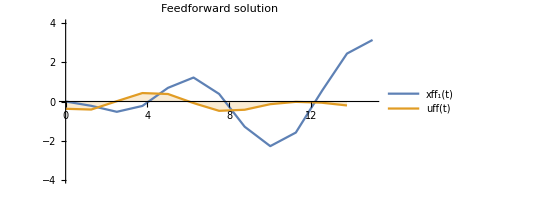

```mathematica
n=12;τ=15;τ1= τ*1.25 ;m = 0.1;M = 1;g = 1;l = 1;
nDim = 2;
Δt=τ/n;
x = {x1,x2};
λ = {λ1,λ2};
fx = {x2,-Sin[x1] + u};
L = 1/2*u^2; (*Cost function*)
{xff,uff} = ffCartPendulumGeneral[n,nDim,x,λ,fx,τ,τ1,L];

p1a=Plot[{Subscript[xff, 1][t],uff[t]},{t,0,τ},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->"Expressions",PlotLabel->"Feedforward solution",AspectRatio->1/2,ImageSize->400,GridLines->{None,{-π,π}}]
```

Rough Work

```mathematica
Clear["Global`*"]; (* Fix Bugs here *)
Remove["Global`*"];

n=20;τ=15;τ1= τ*1.25 ;m = 0.1;M = 1;g = 1;l = 1;
nDim = 2;
Δt=τ/n;
x = {x1,x2};
λ = {λ1,λ2};
xff0 = {xff10,xff20};
xff = {xff1,xff2};
fx = {x2,-Sin[x1] + u};
L = 1/2*u^2; (*Cost function*)
eqn = D[fx,u].λ + D[L,u];
sol = Solve[{eqn==0},{u}][[1]];
{u} = {u}/.sol ;
replacement[j_] := Join[Table[x[[i]] -> Subscript[x[[i]], j],{i,1,nDim}],Table[λ[[i]] -> Subscript[λ[[i]], j],{i,1,nDim}]];
For[i = 0,i<n,i++,Subscript[u, i]= u/.replacement[i]];
λdot = -Grad[fx,x]ᵀ.λ - Grad[L,x]ᵀ;
For[i = 0,i<=n,i++,Subscript[f, i]= Join[fx,λdot]/.replacement[i]]; 
bcs={Subscript[x1, 0]==Subscript[x2, 0]==Subscript[x2, n]==0,Subscript[x1, n]==π}; (* Take the bcs as an input*)eqns=Flatten[Join[bcs,Table[Thread[(Join[x,λ]/.replacement[i])==1/2 Δt (Subscript[f, i-1]+Subscript[f, i])+(Join[x,λ]/.replacement[i-1])],{i,1,n}]]];sv = Flatten[Table[Table[{(Join[x,λ]/.replacement[i])[[j]],0},{j,1,2*nDim}],{i,0,n}],1];
froot=FindRoot[eqns,sv];
For[i = 1,i<=nDim,i++,xff0[[i]] = ListInterpolation[Table[Subscript[x[[i]], j],{j,0,n}]/.froot,{0,τ},InterpolationOrder->1]];uff0=ListInterpolation[Table[Subscript[u, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1]; 

For[i = 1,i<=nDim,i++,xff[[i]][t_]:=Piecewise[{{xff0[[i]][t],0≤t≤τ}},0]];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
```

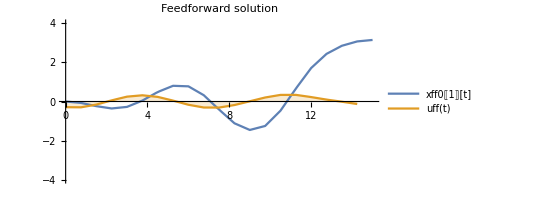

```mathematica
p1a=Plot[{xff0[[1]][t],uff[t]},{t,0,τ},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->"Expressions",PlotLabel->"Feedforward solution",AspectRatio->1/2,ImageSize->400,GridLines->{None,{-π,π}}]
```

Do the same for a simpler system

```mathematica
tempfile=FilenameJoin[{$TemporaryDirectory,"saved.wl"}];
Save[tempfile,S];
```

```mathematica
tempfile=FilenameJoin[{$TemporaryDirectory,"saved.wl"}];
Get[tempfile]; 
S[[1,1]]/.{zero -> 0.00001} (* The original expression had no solution*)
```